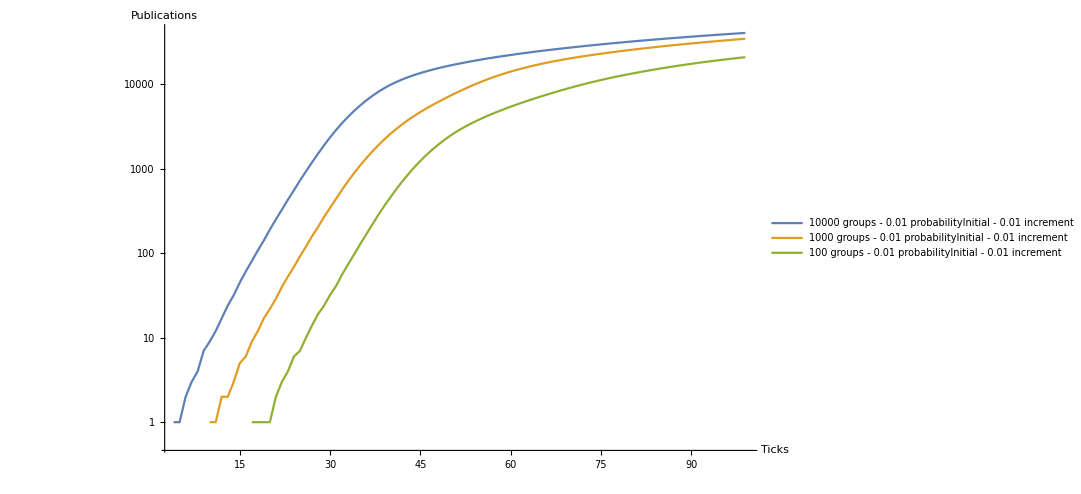

```mathematica
list=Import["/home/fabianact/newTest/NuevoModelo/ModeloConAcumulacion/averageResults/All.csv"];
plot = Show[ListLogPlot[{Partition[list, 100][[1]], Partition[list, 100][[4]], Partition[list, 100][[7]]},ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{"10000 groups - 0.01 probabilityInitial - 0.01 increment", "1000 groups - 0.01 probabilityInitial - 0.01 increment", "100 groups - 0.01 probabilityInitial - 0.01 increment" },PlotRange->All]]
Export["TotalConAcumulacionG1.png",plot];
```

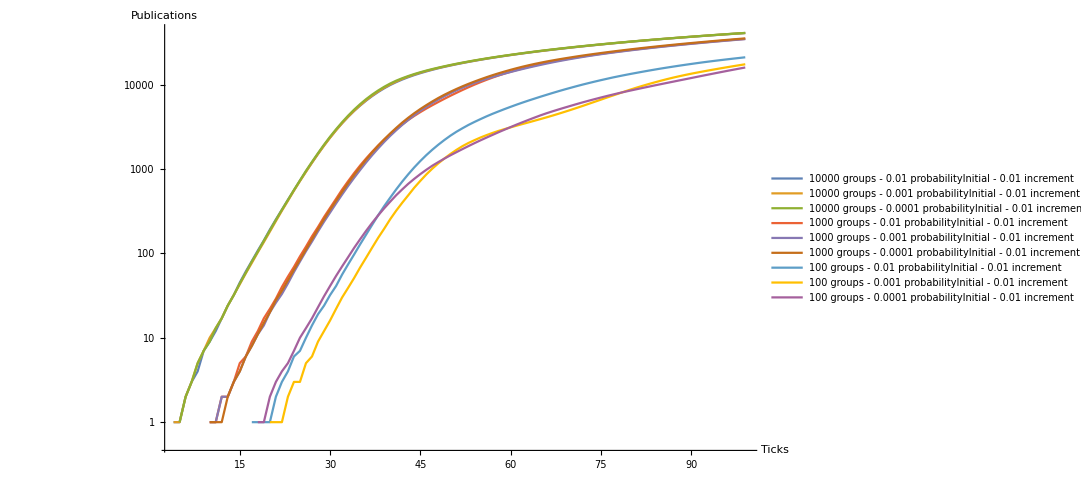

```mathematica
plot = Show[ListLogPlot[{Partition[list, 100][[1]],Partition[list, 100][[10]],Partition[list, 100][[19]], Partition[list, 100][[4]],Partition[list, 100][[13]],Partition[list, 100][[22]], Partition[list, 100][[7]] , Partition[list, 100][[16]], Partition[list, 100][[25]] },ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{"10000 groups - 0.01 probabilityInitial - 0.01 increment","10000 groups - 0.001 probabilityInitial - 0.01 increment", "10000 groups - 0.0001 probabilityInitial - 0.01 increment","1000 groups - 0.01 probabilityInitial - 0.01 increment", "1000 groups - 0.001 probabilityInitial - 0.01 increment","1000 groups - 0.0001 probabilityInitial - 0.01 increment", "100 groups - 0.01 probabilityInitial - 0.01 increment" ,  "100 groups - 0.001 probabilityInitial - 0.01 increment", "100 groups - 0.0001 probabilityInitial - 0.01 increment"   },PlotRange->All]]
Export["TotalConAcumulacionG1.png",plot];
```

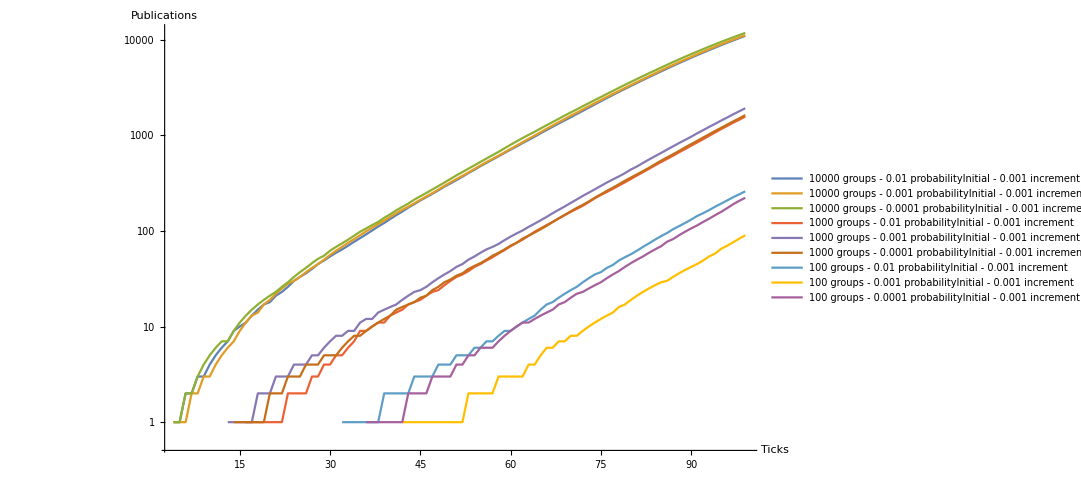

```mathematica
plot = Show[ListLogPlot[{Partition[list, 100][[2]],Partition[list, 100][[11]],Partition[list, 100][[20]], Partition[list, 100][[5]],Partition[list, 100][[14]],Partition[list, 100][[23]], Partition[list, 100][[8]] , Partition[list, 100][[17]], Partition[list, 100][[26]] },ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{"10000 groups - 0.01 probabilityInitial - 0.001 increment","10000 groups - 0.001 probabilityInitial - 0.001 increment", "10000 groups - 0.0001 probabilityInitial - 0.001 increment","1000 groups - 0.01 probabilityInitial - 0.001 increment", "1000 groups - 0.001 probabilityInitial - 0.001 increment","1000 groups - 0.0001 probabilityInitial - 0.001 increment", "100 groups - 0.01 probabilityInitial - 0.001 increment" ,  "100 groups - 0.001 probabilityInitial - 0.001 increment", "100 groups - 0.0001 probabilityInitial - 0.001 increment"   },PlotRange->All]]
Export["TotalConAcumulacionG2.png",plot];
```

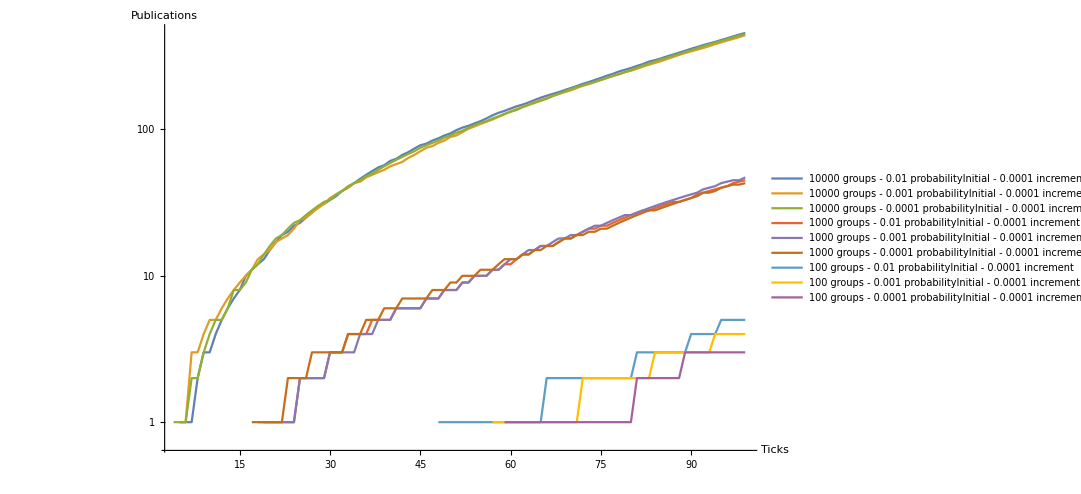

```mathematica
plot = Show[ListLogPlot[{Partition[list, 100][[3]],Partition[list, 100][[12]],Partition[list, 100][[21]], Partition[list, 100][[6]],Partition[list, 100][[15]],Partition[list, 100][[24]], Partition[list, 100][[9]] , Partition[list, 100][[18]], Partition[list, 100][[27]] },ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{"10000 groups - 0.01 probabilityInitial - 0.0001 increment","10000 groups - 0.001 probabilityInitial - 0.0001 increment", "10000 groups - 0.0001 probabilityInitial - 0.0001 increment","1000 groups - 0.01 probabilityInitial - 0.0001 increment", "1000 groups - 0.001 probabilityInitial - 0.0001 increment","1000 groups - 0.0001 probabilityInitial - 0.0001 increment", "100 groups - 0.01 probabilityInitial - 0.0001 increment" ,  "100 groups - 0.001 probabilityInitial - 0.0001 increment", "100 groups - 0.0001 probabilityInitial - 0.0001 increment"   },PlotRange->All]]
Export["TotalConAcumulacionG3.png",plot];
```